# Project report

## Broken Column

D Malan

Department of Chemistry
University of Pretoria

08 February 2020

## Introduction

The column broke. I don’t know when this happened

## Experimental

When I checked the FID signal for the startup checklist, I found no signal.

The hydrogen leak detector showed a major hydrogen leak at the joint between the inlet and the manifold block.

The inlet column nut was loosened, the stop was moved about 20 mm down and the car was eased down. This allowed inspection of the column.

When it was confirmed that the column had broken the coaxial heater assembly was carefully removed to not disturb  any evidence.

A test setup was made to examine the clearances.

## Calculations

```mathematica
r=1
```

1

```mathematica
v=0.5
```

0.5

```mathematica
h
```

h

```mathematica
f[x_]:= Sqrt[r-x^2]
```

```mathematica
g[x_,h_]:= -Sqrt[r-(h-x)^2]+v
```

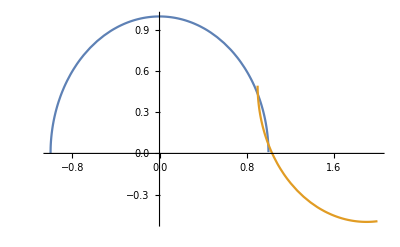

```mathematica
Plot[{f[x],g[x]}, {x, -1,2}]
```

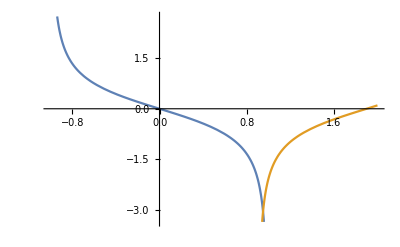

```mathematica
Plot[{f'[x],g'[x]}, {x, -1,2}]
```

```mathematica
Solve[f[x]==g[x,h]&&f'[x]==g'[x,h],{x,h}]
```

{{x→0.95,h→-0.0322168},{x→0.95,h→1.93222}}

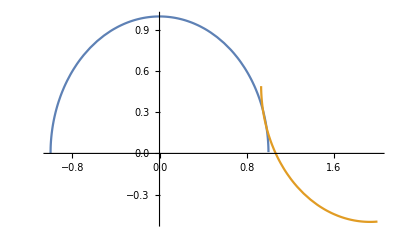

```mathematica
Plot[{f[x],g[x,1.93222]}, {x, -1,2}]
```

Calculation halted.

## Results

The first inspection showed that the column had broken just below the inlet column nut.

The inlet-side rails shifted during disassembly. This is not unusual.

Microscopic examination did not show any overheating at the broken end. When the column was removed,  the polyimide was seen to be a bit darker on the detector end, but not of the portion inside the block.

The photograph shows the clearance. The protrusion from the column nut is the ferrule that’s extruded.

## Discussion

The protrusion of the ferrule had made the gap between the manifold block and the inlet nut very small. There’ s a certain minimum radius that a polyimide-coated fused silica capillary can sustain indefinitely. If the radius is smaller than that, it breaks spontaneously after a time. (I have no reference for this, it’s something I heard somewhere.) Even a small misalignment between the manifold block and inlet would cause a large radius, and it is quite possible that this is what happened.

I’ve seen this happen before, but there was always the possibility that there had been a mechanical event that had caused the break. Today I am sure that nothing had happened between shutting down last night and discovery of the break.

That there are no signs of the column being overheated in the manifold blocks is a good sign. This means that the careful management of  the heating of the blocks during the runs was successful, and this adds evidence to the idea that the column inside the manifold blocks never reach the setpoint temperature during operation.

The aborted calculation above shows that it should not be too difficult to create a simple model of misalignment and column radius.

## Conclusion

The column broke because of insufficient strain relief between the inlet-end manifold block and the inlet nut.

## Recommendations

Replace the column nut and the ferrule with new ones.

Design a system that leave more relief for the column between the manifold blocks and the column and the detector.